-Graphics3D-

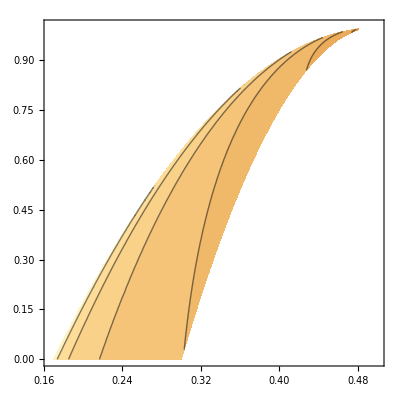

```mathematica
tc=1.0;
pc=1.0/2;
ab=1.0/3;
as=1.0/5;
pb[t_,a_]:=pc-a*Sqrt[1-t/tc];
nc[t_, p_]:=((tc-t)/(p-pb[t,ab]))^2;
Plot3D[Log[nc[t,p]],{p,pc-a,pc},{t,0,tc}]
ContourPlot[Log[nc[t,p]],{p,pc-a,pc},{t,0,tc},RegionFunction->Function[{p,t},pb[t,as]>p> pb[t,ab]]]
```